```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"FEDeriK.m"]
```

# FEDeriK - Functional Equation Derivation Kit

## Exports

```mathematica
SetGlobalSetup::usage="";

FTruncate::usage="";

TakeDerivatives::usage="";

QMeSForm::usage="";

FExpand::usage="";

DExpand::usage="";

MakeClassicalAction::usage="";

WetterichEquation::usage="";

MakeDSE::usage="";

ResolveDerivatives::usage="";
```

```mathematica
Remove["*`F"]
```

```mathematica
AddIndexedObject::usage="";
ShowIndexedObjects::usage="";
AddCorrelationFunction::usage="";
ShowCorrelationFunctions::usage="";
SetGlobalSetup::usage="";
SetUnorderedIndices::usage="";
SetSymmetricObject::usage="";

FEq::usage="";
FTerm::usage="";
F::usage="";
Propagator::usage="";
GammaN::usage="";
R::usage="";
Rdot::usage="";
S::usage="";
ABasis::usage="";
VBasis::usage="";
γ::usage="";
Field::usage="";
FDOp::usage="";
Field::usage="";
FMinus::usage="";
AnyField::usage="";
ResolveFDOp::usage="";
```

## Begin Private

```mathematica
Begin["`Private`"];
```

## Global setup redefinitions

```mathematica
FTruncate[expr_]/;Head[$GlobalSetup]=!=Symbol:=FTruncate[$GlobalSetup,expr];

TakeDerivatives[expr_,derivativeList_]/;Head[$GlobalSetup]=!=Symbol:=TakeDerivatives[$GlobalSetup,expr,derivativeList,"Symmetries"->{}];

TakeDerivatives[expr_,derivativeList_,OptionsPattern[]]/;Head[$GlobalSetup]=!=Symbol:=TakeDerivatives[$GlobalSetup,expr,derivativeList,"Symmetries"->OptionValue["Symmetries"]];

QMeSForm[expr_]/;Head[$GlobalSetup]=!=Symbol:=QMeSForm[$GlobalSetup,expr];

FExpand[expr_,order_Integer]/;Head[$GlobalSetup]=!=Symbol:=FExpand[$GlobalSetup,expr,order];

DExpand[expr_,order_Integer]/;Head[$GlobalSetup]=!=Symbol:=DExpand[$GlobalSetup,expr,order];

MakeClassicalAction[]/;Head[$GlobalSetup]=!=Symbol:=MakeClassicalAction[$GlobalSetup];

MakeDSE[field_]/;Head[$GlobalSetup]=!=Symbol:=MakeDSE[$GlobalSetup,field];

ResolveDerivatives[expr_]/;Head[$GlobalSetup]=!=Symbol:=ResolveDerivatives[$GlobalSetup,expr,"Symmetries"->{}];

ResolveDerivatives[expr_,OptionsPattern[]]/;Head[$GlobalSetup]=!=Symbol:=ResolveDerivatives[$GlobalSetup,expr,"Symmetries"->OptionValue["Symmetries"]];

ResolveFDOp[expr_]/;Head[$GlobalSetup]=!=Symbol:=ResolveFDOp[$GlobalSetup,expr];
```

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

ModuleLoaded[FEDeriK]=True;
```

```mathematica
$userCorrelationFunctions={};
$userIndexedObjects={};
$userOrderedObjects={};

$CorrelationFunctions:={Propagator,GammaN}∪$userCorrelationFunctions;
$OrderedObjects:=$CorrelationFunctions∪{R,Rdot,S}∪$userOrderedObjects;
$indexedObjects:=$OrderedObjects∪{ABasis,VBasis,γ,Field}∪$userIndexedObjects;
$allObjects:={FMinus}∪$indexedObjects

$nonCommutingObjects:=$CorrelationFunctions∪{FDOp,Field};

$MaxDerivativeIterations=500;
$CanonicalOrdering="f>af>b";

Protect@@$allObjects;
```

```mathematica
AddIndexedObject[name_Symbol]:=Module[{},
AppendTo[$userIndexedObjects,name];
$userIndexedObjects=DeleteDuplicates[$userIndexedObjects];
Protect@@$allObjects;
];
ShowIndexedObjects[]:=Print[TableForm[Sort@$indexedObjects]]

AddOrderedObject[name_Symbol]:=Module[{},
AppendTo[$userOrderedObjects,name];
$userOrderedObjects=DeleteDuplicates[$userOrderedObjects];
Protect@@$allObjects;
];
ShowOrderedObjects[]:=Print[TableForm[Sort@$userOrderedObjects]]

AddCorrelationFunction[name_Symbol]:=Module[{},
AppendTo[$userCorrelationFunctions,name];
$userCorrelationFunctions=DeleteDuplicates[$userCorrelationFunctions];
Protect@@$allObjects;
];
ShowCorrelationFunctions[]:=Print[TableForm[Sort@$CorrelationFunctions]]
```

```mathematica
Protect[$GlobalSetup];

SetGlobalSetup[setup_]:=Module[{},
AssertFSetup[setup];

Unprotect[$GlobalSetup];
$GlobalSetup=setup;
Protect[$GlobalSetup];
];

SetGlobalSetup[]:=Module[{},
Unprotect[$GlobalSetup];
ClearAll[$GlobalSetup];
Protect[$GlobalSetup];
]
```

## FDOp, FTerm and FEq definitions

### Basic definitions

```mathematica
F[expr___]:=FEq[FTerm[expr]]
```

```mathematica
type::error="The expression given is neither an FEq nor an FTerm.";
```

```mathematica
Unprotect[FTerm];
ClearAll[FTerm];

FTimesPowerPatternaToFTermb=Power[a,FTerm[b_]];
FTimesPowerPatternFTermbtoa=Power[a,FTerm[b_]];

FTerm::TimesError="An FTerm cannot be multiplied using Times[__]. To multiply FTerms, use term1**term2, also with scalars, a**term. Error in expression
`1`";
FTerm::FTermPowerError="An FTerm cannot be taken to a power of an FTerm.";

(*Multiplication of FTerms. *)
FTerm/:NonCommutativeMultiply[FTerm[a__],FTerm[b__]]:=FTerm[a,b]
FTerm/:NonCommutativeMultiply[FTerm[],FTerm[b__]]:=FTerm[b]
FTerm/:NonCommutativeMultiply[FTerm[b__],FTerm[]]:=FTerm[b]
FTerm/:NonCommutativeMultiply[a_,FTerm[b__]]/;NumericQ[a]:=FTerm[a,b]

FTerm[pre___,NonCommutativeMultiply[in___],post___]:=FTerm[pre,in,post]
FTerm[pre___,Times[inpre__,NonCommutativeMultiply[in___],inpost__],post___]:=FTerm[pre,inpre*inpost,in,post]

FTerm[1,post___]:=FTerm[post]

couldBeField=MatchQ[#,_Symbol[_Symbol]]||MatchQ[#,_Symbol[-_Symbol]]||MatchQ[#,_Symbol[{_,_List}]]||MatchQ[#,_Symbol[{_,_List}]]&;
isFreeTerm=Not@(ContainsAny[GetAllSymbols[#],$nonCommutingObjects]||Or@@Map[couldBeField,#,Infinity])&;

FTerm[first_,pre___,Times[a_,other2_],post___]/;NumericQ[first]&&NumericQ[a]:=FTerm[first*a,pre,other2,post]
FTerm[first_,pre___,Times[a_,other2_],post___]/;Not@NumericQ[first]&&NumericQ[a]:=FTerm[a,first,pre,other2,post]

FTerm[first_,pre___,a_,post___]/;NumericQ[first]&&NumericQ[a]:=FTerm[first*a,pre,post]
FTerm[first_,pre___,a_,post___]/;Not[NumericQ[first]]&&NumericQ[a]:=FTerm[a,first,pre,post]

(*Some reduction for FTerm[]*)
FTerm/:FTerm[]*FTerm[a_]:=FTerm[a]
FTerm/:Plus[FTerm[],FTerm[b_]]/;NumericQ[b]:=FTerm[1+b];
FTerm/:Power[FTerm[],n_]:=FTerm[]
FTerm/:Times[a_,FTerm[]]:=FTerm[a];
FTerm/:Power[FTerm[a_],b_]/;NumericQ[a]&&NumericQ[b]:=FTerm[Power[a,b]];FTerm/:Plus[FTerm[a_],FTerm[b_]]/;NumericQ[a]&&NumericQ[b]:=FTerm[a+b];
FTerm/:Times[FTerm[a_],FTerm[b_]]/;NumericQ[a]&&NumericQ[b]:=FTerm[a*b];

(*Pre-reduction of zero FTerms*)
FTerm[___,0,___]:=FTerm[0]
FTerm[pre___,FTerm[],post___]:=FTerm[pre,post]

(*Reduction of immediately nested FTerms*)
FTerm[pre___,FTerm[in__],post___]:=FTerm[pre,in,post] 

Protect[FTerm];
```

```mathematica
Unprotect[FEq];
ClearAll[FEq];

FEq::TimesError="A FEq cannot be multiplied using Times[__]. To multiply FEqs, use eq1**eq2, also with scalars, a**eq. Error in expression
`1`";

(*Removal of zero FTerms*)
FEq[pre___,FTerm[___,0,___],post___]:=FEq[pre,post]
FEq[pre___,FTerm[],mid___,FTerm[],post___]:=FEq[FTerm[2],pre,mid,post]
FEq[pre___,FTerm[a_],mid___,FTerm[b_],post___]/;NumericQ[a]&&NumericQ[b]:=FEq[FTerm[a+b],pre,mid,post]
FEq[pre___,FTerm[],mid___,FTerm[a_],post___]/;NumericQ[a]:=FEq[FTerm[a+1],pre,mid,post]
FEq[pre___,FTerm[a_],mid___,FTerm[],post___]/;NumericQ[a]:=FEq[FTerm[a+1],pre,mid,post]

(*Sum splitting of FTerms*)
FEq[preEq___,FTerm[preTerm___,Plus[a_,b__],postTerm___],postEq___]:=FEq[preEq,FTerm[preTerm,a,postTerm],FTerm[preTerm,Plus[b],postTerm],postEq]

(*Sums of FTerms*)
FEq[preEq___,Plus[FTerm[a__],FTerm[b__],c___],postEq___]:=FEq[preEq,FTerm[a],Plus[FTerm[b],c],postEq]
FEq/:Plus[FEq[a___],FTerm[b__]]:=FEq[a,FTerm[b]]

(*Sums of FEqs*)
FEq/:Plus[preEq___,FEq[terms1___],midEq___,FEq[terms2___],postEq___]:=Plus[preEq,midEq,postEq,FEq[terms1,terms2]]

(*Multiplication of FEqs*)
FEq/:Times[pre___,FEq[a__],post___]:=(Message[FEq::TimesError,{pre,FEq[a],post}];Abort[])
FEq[prefeq__,Times[pre___,FTerm[a__],post___],postfeq__]:=(Message[FTerm::TimesError,{pre,FTerm[a],post}];Abort[])

FEq/:NonCommutativeMultiply[FTerm[b__],FEq[c__]]:=FEq[Map[FTerm[b]**#&,FEq[c]]]
FEq/:NonCommutativeMultiply[FEq[c__],FTerm[b__]]:=FEq[Map[#**FTerm[b]&,FEq[c]]]
FEq/:NonCommutativeMultiply[FEq[a__],FEq[b__]]:=FEq@@(Flatten@Table[FEq[{a}[[i]]**{b}[[j]]],{i,1,Length[{a}]},{j,1,Length[{b}]}])

(*Removing zeros and ones*)
FEq/:NonCommutativeMultiply[FTerm[b___],FEq[]]:=FEq[]

FEq/:NonCommutativeMultiply[FTerm[],FEq[b___]]:=FEq[b]
FEq/:NonCommutativeMultiply[FEq[b___],FTerm[]]:=FEq[b]

FEq/:NonCommutativeMultiply[FTerm[0],FEq[b___]]:=FEq[]
FEq/:NonCommutativeMultiply[FEq[b___],FTerm[0]]:=FEq[]

FEq[pre___,0,post___]:=FEq[pre,post]

FEq/:FTerm[FEq[a__]]:=FEq[a];
FEq/:FTerm[FEq[a__],FEq[b__]]:=FEq@@(Flatten@Table[FEq[{a}[[i]]**{b}[[j]]],{i,1,Length[{a}]},{j,1,Length[{b}]}])

(*Reduction of immediately nested FEqs*)
FEq[pre___,FEq[in___],post___]:=FEq[pre,in,post]

FEq/:FTerm[FEq[a__]]:=FEq[a]
FEq/:FTerm[pre___,FEq[a__],post___]:=NonCommutativeMultiply[FTerm[pre],FEq[a],FTerm[post]]

(*Expand nested FEq in sub-terms*)
FEq[pre___,FTerm[prein___,FEq[in___],postin___],post___]:=FEq[pre,NonCommutativeMultiply[FTerm[prein],FEq[in],FTerm[postin]],post]

Protect[FEq];
```

### Checks and assertions

#### FTerm and FEq

```mathematica
FTermQ[expr_]:=Head[expr]===FTerm;
FTerm::notFTerm="The term `1` is not an FTerm.";
AssertFTerm[expr_]:=If[Not@FTermQ[expr],Message[FTerm::notFTerm,expr];Abort[]];

FEqQ[expr_]:=Head[expr]===FEq;
FEq::notFEq="The term `1` is not an FEq.";
AssertFEq[expr_]:=If[Not@FEqQ[expr],Message[FEq::notFEq,expr];Abort[]];
```

#### FMinus

```mathematica
Unprotect[FMinus];
ClearAll[FMinus];

(*Grassmann minus signs do not care about index positioning. We force them always up*)
FMinus[{a_,b_},{Times[-1,ia_],ib_}]:=FMinus[{a,b},{ia,ib}]
FMinus[{a_,b_},{ia_,Times[-1,ib_]}]:=FMinus[{a,b},{ia,ib}]

(*Powers are simple*)
FMinus/:Power[FMinus[{a_,b_},{ia_,ib_}],n_Integer]/;EvenQ[n]:=1
FMinus/:Power[FMinus[{a_,b_},{ia_,ib_}],n_Integer]/;OddQ[n]:=FMinus[{a,b},{ia,ib}]

Protect[FMinus];
```

#### Field Space

```mathematica
(* Check if a given field definition is valid. Can be either its own anti-field or a pair {af,f} *)
FieldDefQ[expr_]:=Module[{},
If[Head[expr]===List,
If[Length[expr]=!=2,
Print["A field definition must be either of form f[x...] or {af[x...],f[x...]}. \"",expr,"\" does not fit."];Return[False]];

If[Head[expr[[1]]]===Head[expr[[2]]],
Print["A field definition {af[x...],f[x...]} must have different field names af and f. \"",expr,"\" does not fit."];
Return[False]];

If[Not@(List@@(expr[[1]])===List@@(expr[[2]])),
Print["A field definition {af[x...],f[x...]} must have identical indices. \"",expr,"\" does not fit."];
Return[False]];

Do[
If[Not@(MatchQ[expr[[i]],_Symbol[_,{__Symbol}]]||MatchQ[expr[[i]],_Symbol[_]]),
Print["A field definition f[x...] must have indices f[p] or f[p,{a,b,...}]. \"",expr[[i]],"\" does not fit."];
Return[False]],
{i,1,2}
];

Return[True];
];

If[Not@(MatchQ[expr,_Symbol[_,{__Symbol}]]||MatchQ[expr,_Symbol[_]]),
Print["A field definition f[x...] must have indices f[p] or f[p,{a,b,...}]. \"",expr,"\" does not fit."];
Return[False]];

Return[True];
];

FieldDef::invalidFieldDefinition="The given field definition `1` is not valid.";

AssertFieldDef[expr_]:=If[Not@FieldDefQ[expr],
Message[FieldDefinition::invalidFieldDefinition];
Abort[]];
```

```mathematica
(* Check if a given field space definition is valid *)
FieldSpaceDefQ[fieldSpace_]:=Module[{},
If[Head[fieldSpace]=!=Association,Print["An FSetup must be an association"];Return[False]];

If[Not@(Keys[fieldSpace]==={"cField","Grassmann"}),
Print["fields must contain the two keys {\"cField\",\"Grassmann\"}!"];
Return[False]];

If[Not@ListQ[fieldSpace["cField"]],
Print["fields[\"cField\"] must be a list!"];
Return[False]];

If[Not@(And@@Map[FieldDefQ,fieldSpace["cField"]]),
Print["fields[\"cField\"] must contain valid fields!"];
Return[False]];

If[Not@ListQ[fieldSpace["Grassmann"]],
Print["fields[\"Grassmann\"] must be a list!"];
Return[False]];

If[Not@(And@@Map[FieldDefQ,fieldSpace["Grassmann"]]),
Print["fields[\"Grassmann\"] must contain valid fields!"];
Return[False]];

Return[True];
];

FieldSpaceDefinition::invalidFieldDefinition="The given field space definition is invalid.";

AssertFieldSpaceDef[fields_]:=If[Not@FieldSpaceDefQ[fields],
Message[FieldSpaceDefinition::invalidFieldDefinition];Abort[]];
```

#### FSetup

```mathematica
FSetup::notFSetup="The given setup is not valid!";

FSetupQ[setup_]:=Module[{},
If[Not@(Head[setup]===Association),
Print["A valid setup must be an Association!"];
Return[False]];

If[Not@MemberQ[Keys[setup],"FieldSpace"],
Print["A valid setup must have the key \"FieldSpace\"!"];
Return[False]];

If[Not@FieldSpaceDefQ[setup["FieldSpace"]],
Return[False]];

Return[True];
];

AssertFSetup[setup_]:=Module[{},
If[Not@(Head[setup]===Association),
Print["A valid setup must be an Association!"];
Message[FSetup::notFSetup];
Abort[]];

If[Not@MemberQ[Keys[setup],"FieldSpace"],
Print["A valid setup must have the key \"FieldSpace\"!"];
Message[FSetup::notFSetup];
Abort[]];

AssertFieldSpaceDef[setup["FieldSpace"]];
];
```

#### Existence of a field

```mathematica
(* Check if a given field definition is valid. Can be either its own anti-field or a pair {af,f} *)
FieldQ[setup_,expr_]:=Module[{},
If[Not@MatchQ[expr,_Symbol[_Symbol]]&&Not@MatchQ[expr,_Symbol[-_Symbol]]&&Not@MatchQ[expr,_Symbol[_List]],
Print["A field f must have a single super-index f[i]. \"",expr,"\" does not fit."];
Return[False]];

If[Not@(MemberQ[Map[Head,setup["FieldSpace"]//Values//Flatten],Head[expr]]),
Print["The field \"",expr,"\" is not present in the given field space."];
Return[False]];

Return[True];
];

Field::invalidField="The given field `1` does not exist.";

AssertField[setup_,expr_]:=If[Not@FieldQ[setup,expr],
Message[FieldDefinition::invalidField];
Abort[]];
```

#### Derivative List

```mathematica
(*Check a derivative list for correct formatting.*)
DerivativeListQ[setup_,derivativeList_]:=Module[{},

If[Not@(Head[derivativeList]===List),
Print["A valid derivativeList must be an List!"];
Return[False]];

If[Not@AllTrue[derivativeList,FieldQ[setup,#]&],
Print["A valid derivativeList must be an List of fields f_[p_,{___}] of f_[p_] which have been defined in the setup!"];
Return[False]];

Return[True];
];

DeriveEquation::invalidDerivativeList="The given derivativeList `1` is not valid.";

AssertDerivativeList[setup_,expr_]:=If[Not@DerivativeListQ[setup,expr],
Message[DeriveEquation::invalidDerivativeList];
Abort[]];
```

#### FDOp

```mathematica
Unprotect[FDOp];
ClearAll[FDOp];

FDOp::invalid="`1` is not a valid FDOp.";
FDOp::invalidArguments="`1` is not a valid FDOp. FDOp takes a single field with an index as argument.";
FDOp::arithmetic="An FDOp cannot be included as anything but a factor in an FTerm. Error in 
  `1`";

FDOp/:Times[a___,FDOp[b___],c___]:=(Message[FDOp::arithmetic,StringTake[ToString@(Hold@Times[a,FDOp[b],c]),{6,-2}]];Abort[])
FDOp/:Plus[a___,FDOp[b___],c___]:=(Message[FDOp::arithmetic,StringTake[ToString@(Hold@Plus[a,FDOp[b],c]),{6,-2}]];Abort[])

FDOp[a_,b__]:=(Message[FDOp::invalidArguments,StringTake[ToString@(Hold@FDOp[a,b]),{6,-2}]];Abort[])

FDOpQ[setup_,expr_]:=(Head[expr]===FDOp)&&MatchQ[expr,(_[_,{__}]|_[_])]&&FieldQ[setup,#]&@@expr;
AssertFDOp[setup_,expr_]:=If[Not@FDOpQ[setup,expr],Message[FDOp::invalid,expr];Abort[]];

Protect[FDOp];
```

## Utilities

#### Getting symbols

```mathematica
exclusions[a_]:=And@@{a=!=List,a=!=Complex,a=!=Plus,a=!=Power,a=!=Times}
GetAllSymbols[expr_]:=DeleteDuplicates@Cases[
Flatten[{expr}//.Times[a_,b__]:>{a,b}//.a_Symbol[b__]/;exclusions[a]:>{a,b}],
_Symbol,
Infinity]
```

### FunctionalD

```mathematica
FunctionalD::malformed="Cannot take a derivative of `1`. Expression is either malformed or this is a bug.";

ClearAll[FunctionalD]
FunctionalD[setup_,expr_,v:(f_[_]|{f_[_],_Integer})..,OptionsPattern[]]:=Internal`InheritedBlock[
{f,nonConst},

Unprotect[f];

nonConst=DeleteDuplicates@Sort@({f,Power}∪$CorrelationFunctions);

(*Rule for normal functional derivatives*)
f/:D[f[x_],f[y_],NonConstants->nonConst]:=γ[{f,f},{-y,x}];
(*Rule for normal functional derivatives, but AnyField*)
f/:D[AnyField[x_],f[y_],NonConstants->nonConst]:=γ[{f,AnyField},{-y,x}];
(*Rule for taking derivatives with AnyField*)
If[f===AnyField,
Map[
(f/:D[#[x_],f[y_],NonConstants->nonConst]:=γ[{f,#},{-y,x}])&
,GetAllFields[setup]
];
];
(*Ignore fields without indices. These are usually tags*)
f/:D[f,f[y_],NonConstants->nonConst]:=0;(*δ[#,y]&;*)

(*Derivative rules for Correlation functions*)
Map[
(f/:D[#[{a__},{b__}],f[if_],NonConstants->nonConst]:=#[{f,a},{-if,b}])&,
$CorrelationFunctions
];

(*Special derivative rule for Propagator*)
f/:D[Propagator[{b_,a_},{ib_,ia_}],f[if_],NonConstants->nonConst]:=Module[
{ic,id,ie,ig},
ic=Symbol@SymbolName@Unique["i"];
id=Symbol@SymbolName@Unique["i"];
ie=Symbol@SymbolName@Unique["i"];
ig=Symbol@SymbolName@Unique["i"];
((-1)FMinus[{a,a},{id,id}]FMinus[{f,b},{if,ib}])**
Propagator[{b,AnyField},{ib,ic}]**
GammaN[{AnyField,f,AnyField},{-ic,-if,-id}]**
Propagator[{AnyField,a},{id,ia}]
];

(*No derivatives of FTerm, FEq*)
f/:D[FTerm[a___],f[y_],NonConstants->nonConst]:=(Message[FunctionalD::malformed,FTerm[a]];Abort[]);
f/:D[FEq[a___],f[y_],NonConstants->nonConst]:=(Message[FunctionalD::malformed,FEq[a]];Abort[]);

(*Chain rules*)
f/:D[g_[FTerm[a___]],f[y_],NonConstants->nonConst]:=(FTerm[g'[FTerm[a]]]**FTerm[FDOp[f[y]],a]);
f/:D[Power[FTerm[a___],b_],f[y_],NonConstants->nonConst]:=(FTerm[b,Power[FTerm[a],b-1]]**FTerm[FDOp[f[y]],a]);
f/:D[Power[a_,FTerm[b___]],f[y_],NonConstants->nonConst]:=(FTerm[Log[a],Power[a,FTerm[b]]]**FTerm[FDOp[f[y]],b]);

Protect[f];

D[expr,v,NonConstants->nonConst]
];

FunctionalD[setup_,expr_,v:(f_[_List,_List]|{f_[_List,_List],_Integer})..,OptionsPattern[]]:=Internal`InheritedBlock[
{f,nonConst},

nonConst=DeleteDuplicates@Sort@({f,Power}∪$CorrelationFunctions);

(*Rule for normal functional derivatives*)
f/:D[f[{f1_,f2_},{i_,j_}],f[{f3_,f4_},{k_,l_}],NonConstants->nonConst]:=γ[{f1,f3},{-k,i}]γ[{f2,f4},{-l,j}];
(*Rule for normal functional derivatives, but AnyField*)

(*No derivatives of FTerm, FEq*)
f/:D[FTerm[a___],f[y_],NonConstants->nonConst]:=(Message[FunctionalD::malformed,FTerm[a]];Abort[]);
f/:D[FEq[a___],f[y_],NonConstants->nonConst]:=(Message[FunctionalD::malformed,FEq[a]];Abort[]);

D[expr,v,NonConstants->nonConst]
];

FunctionalD::badArgumentFTerm="Cannot take derivative of an FTerm. Use TakeDerivatives instead.";
FunctionalD[setup_,FTerm[expr_],v:(f_[__]|{f_[__],_Integer})..,OptionsPattern[]]:=(Message[FunctionalD::badArgumentFTerm];Abort[]);

FunctionalD::badArgumentFEq="Cannot take derivative of an FEq. Use TakeDerivatives instead.";
FunctionalD[setup_,FEq[___],v:(f_[__]|{f_[__],_Integer})..,OptionsPattern[]]:=(Message[FunctionalD::badArgumentFEq];Abort[]);
```

### Symmetries

```mathematica
SetSymmetricObject[obj_,{f__}]:=Module[{},
Unprotect[obj];
obj[{f},{any__}]/;Not@OrderedQ[{any}]:=obj[{f},Sort@{any}];
Protect[obj];
];
SetSymmetricObject[obj_,{f__},{i__Integer}]:=Module[{},
Unprotect[obj];
obj[{f},{any__}]/;Not@OrderedQ[{any}[[{i}]]]:=Module[{new={any}},
new[[{i}]]=Sort@new[[{i}]];
obj[{f},new]
];
Protect[obj];
];
```

### Field and index information

#### Fields

```mathematica
GetcFields[setup_]:=Map[
If[Head[#]===List,Head[#[[2]]],Head[#]]&,
setup["FieldSpace"]["cField"]
];
GetAnticFields[setup_]:=Select[Map[
If[Head[#]===List,Head[#[[1]]],{}]&,
setup["FieldSpace"]["cField"]
],#=!={}&];

GetFermions[setup_]:=Map[
If[Head[#]===List,Head[#[[2]]],Head[#]]&,
setup["FieldSpace"]["Grassmann"]
];
GetAntiFermions[setup_]:=Select[Map[
If[Head[#]===List,Head[#[[1]]],{}]&,
setup["FieldSpace"]["Grassmann"]
],#=!={}&];

GetCommuting[setup_]:=Flatten@Select[Map[
If[Head[#]===List,{Head[#[[1]]],Head[#[[2]]]},Head[#]]&,
setup["FieldSpace"]["cField"]
],#=!={}&];

GetAntiCommuting[setup_]:=Flatten@Select[Map[
If[Head[#]===List,{Head[#[[1]]],Head[#[[2]]]},Head[#]]&,
setup["FieldSpace"]["Grassmann"]
],#=!={}&];
```

```mathematica
GetFieldPairs[setup_]:=GetFieldPairs[setup]=Map[{Head[#[[1]]],Head[#[[2]]]}&,
Select[
Join[setup["FieldSpace"]["Grassmann"],setup["FieldSpace"]["cField"]],
Head[#]===List&
]
];

GetSingleFields[setup_]:=GetSingleFields[setup]=Map[Head[#]&,Select[
Join[setup["FieldSpace"]["Grassmann"],setup["FieldSpace"]["cField"]],
Head[#]=!=List&
]
];

GetAllFields[setup_]:=GetAllFields[setup]=Join[Flatten@GetFieldPairs[setup],GetSingleFields[setup]];

HasPartnerField[setup_,field_]:=HasPartnerField[setup,field]=MemberQ[
Flatten@GetFieldPairs[setup],
field
];
HasPartnerField[setup_,field_[__]]:=HasPartnerField[setup,field];

IsFermion[setup_,field_]:=IsFermion[setup,field]=MemberQ[GetFermions[setup],field];
IsFermion[setup_,field_[__]]:=IsFermion[setup,field];

IsAntiFermion[setup_,field_]:=IsAntiFermion[setup,field]=MemberQ[GetAntiFermions[setup],field];
IsAntiFermion[setup_,field_[__]]:=IsAntiFermion[setup,field];

IscField[setup_,field_]:=IscField[setup,field]=MemberQ[GetcFields[setup],field];
IscField[setup_,field_[__]]:=IscField[setup,field];

IsAnticField[setup_,field_]:=IsAnticField[setup,field]=MemberQ[GetAnticFields[setup],field];
IsAnticField[setup_,field_[__]]:=IsAnticField[setup,field];

IsGrassmann[setup_,field_]:=IsGrassmann[setup,field]=IsFermion[setup,field]||IsAntiFermion[setup,field];
```

```mathematica
GetPartnerField[setup_,field_Symbol]:=GetPartnerField[setup,field]=Module[{pairs,sel},
If[Not@HasPartnerField[setup,field],Return[field]];

pairs=GetFieldPairs[setup];

sel=Select[pairs,MemberQ[#,field,Infinity]&][[1]];
sel=DeleteCases[sel,field];
If[Length[sel]>0,Return[sel[[1]]]];

Print["field ",field," not found!"];Abort[];
];
GetPartnerField[setup_,field_Symbol[i__]]:=GetPartnerField[setup,field][i]
```

#### Checking field content of expressions

```mathematica
ExtractFields[setup_Association,expr_]:=Module[{},
Return@(DeleteDuplicates[Head/@Cases[{expr},
Alternatives@@Map[Blank,GetAllFields[setup]],
Infinity
]]);
];
ExtractFieldsWithIndex[setup_Association,expr_]:=Module[{},
Return@Cases[{expr},
Alternatives@@Map[Blank,GetAllFields[setup]],
Infinity
];
];
```

```mathematica
ContainsGrassmann[setup_Association,expr_]:=Module[{},
Return@
AnyTrue[ExtractFields[setup,expr],IsFermion[setup,#]||IsAntiFermion[setup,#]&];
]
GrassmannCount[setup_Association,expr_]:=Module[{},
Return[Length@
Select[ExtractFieldsWithIndex[setup,expr],IsFermion[setup,Head[#]]||IsAntiFermion[setup,Head[#]]&]
];
]
```

#### Indices

```mathematica
(*Get a list of all unique super-indices within the expression expr*)
GetAllSuperIndices[setup_,expr_FTerm]:=Module[{idxO,idxF},
idxO=Cases[expr,
Alternatives@@(Map[Blank[#]&,$indexedObjects]),
{1,2}];
idxF=Cases[expr,
Alternatives@@(Map[Blank[#]&,GetAllFields[setup]]),
{1,2}];
Return[makePosIdx/@(idxF[[All,1]]∪Join@@idxO[[All,2]])//DeleteDuplicates]
];
GetAllSuperIndices[setup_Association,expr_FEq]:=Module[{},
Return@(GetAllSuperIndices[setup,#]&/@(List@@expr))
];
```

```mathematica
ExtractObjectsWithIndex[setup_Association,expr_FTerm]:=Module[{},
Return@Cases[expr,
Alternatives@@(Map[Blank[#]&,{AnyField}∪$indexedObjects∪GetAllFields[setup]]),
{1,2}];
];
ExtractObjectsWithIndex[setup_Association,expr_FEq]:=Module[{},
Return@(
(ExtractObjectsWithIndex[setup,#]&/@(List@@expr))
)
];
```

```mathematica
ExtractObjectsAndIndices[setup_,expr_FTerm]:=Module[{idxO,idxF},
idxO=Cases[expr,
Alternatives@@(Map[Blank[#]&,$indexedObjects]),
{1,2}];
idxF=Cases[expr,
Alternatives@@(Map[Blank[#]&,Join[GetAllFields[setup],{AnyField}]]),
{1,2}];
Return[{
Join[idxO,idxF],
makePosIdx/@Join[idxF[[All,1]],Join@@idxO[[All,2]]]//DeleteDuplicates
}]
];
ExtractObjectsAndIndices[setup_Association,expr_FEq]:=Module[{},
Return@DeleteDuplicates@({Flatten[#[[All,1]]],Join@@#[[All,2]]}&@
(ExtractObjectsAndIndices[setup,#]&/@(List@@expr))
)
];
```

```mathematica
SuperIndices::undeterminedSums="There are indices with count > 2 in the expression
    `1`
This is not allowed for valid terms/equation. Problematic indices:
    `2`";
```

```mathematica
(*Get a list of all closed super-indices within the expression expr*)
GetClosedSuperIndices[setup_,expr_]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];
indices=Select[indices,Head[#]=!=List&];
count=Map[Count[objects,#,{1,5}]&,indices];

Return[
Pick[indices,
Map[Mod[#,2]===0&,count]
]
];
];
```

```mathematica
(*Get a list of all open super-indices within the expression expr*)
GetOpenSuperIndices[setup_,expr_]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];
indices=Select[indices,Head[#]=!=List&];
count=Map[Count[objects,#,Infinity]&,indices];

Return[
Pick[indices,
Map[Mod[#,2]=!=0&,count]
]
];
];
```

```mathematica
(*Check whether all indices are closed within expr. 
This disallows also multiple use of a single index name, !anywhere!*)
AllSuperIndicesClosed[setup_,expr_FTerm]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];

count=Map[Count[objects,#,Infinity]&,indices];
Return[AllTrue[count,#==2&]];
];
AllSuperIndicesClosed[setup_,expr_FEq]:=And@@(AllSuperIndicesClosed[setup,#]&/@expr)
AllSuperIndicesClosed[setup_,expr_]:=(Message[type::error];Abort[])

SuperIndicesValid[setup_,expr_FTerm]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];
indices=Select[indices,Head[#]=!=List&];
count=Map[Count[objects,#,Infinity]&,indices];

If[AnyTrue[count,#>2&],Message[SuperIndices::undeterminedSums,expr,Pick[indices,#>2&/@count]];Return[False]];
Return[True];
];
SuperIndicesValid[setup_,expr_FEq]:=SuperIndicesValid[setup,#]&/@expr
SuperIndicesValid[setup_,expr_]:=(Message[type::error];Abort[])
```

```mathematica
replFields[setup_]:=replFields[setup]=Dispatch@Module[{allFields},
allFields=Join[GetAllFields[setup],{AnyField}];
Join[
Thread[(#[a_]&/@allFields):>Evaluate[(Field[{#},{a}]&/@allFields)]],
Thread[(#[a_,b_List]&/@allFields):>Evaluate[(Field[{#},{{a,b}}]&/@allFields)]]
]
];
unreplFields[setup_]:=unreplFields[setup]=Dispatch@Thread[(Field[{#},{a_}]&/@GetAllFields[setup]):>Evaluate[(#[a]&/@GetAllFields[setup])]]
```

```mathematica
GetSuperIndexTermTransformations::momentumConservation="Momentum conservation for the momentum `1` has been violated.";
GetSuperIndexTermTransformations::multiContraction="The indices `1` have been contracted with more than one other object.";

Unprotect[$momentum,$groupIndex];
$momentum[-i_]:=-$momentum[i];
Protect[$momentum,$groupIndex];

GetSuperIndexTermTransformations::usage="Returns a set {fw,bw}, where fw is a transformation from explicit to super indices, and bw the backwards transformation.
fw is a list of three lists. The fw[[1]] is a list that transforms the explicit index lists as they occur in the given expression, fw[[2]] transforms the momenta, fw[[3]] transforms the group indices. bw has the same structure.";

GetSuperIndexTermTransformationsSingleFTerm[setup_,term_FTerm]:=Module[
{doFields,undoFields,kdx,
allObj,idx,jdx,newObj,indexPosToChange,indicesToChange,newSuperIndices,
repl,
replForward,replBackward},

(*Get all objects and bring them in standard form*)
doFields=replFields[setup];
undoFields=unreplFields[setup];
allObj=ExtractObjectsWithIndex[setup,term]/.doFields/.a_[f_,i_]/;MemberQ[$allObjects,a]:>a[Transpose[{f,i}]];

(*We find all positions where indices are given explicitly*)
indexPosToChange=
Map[
Join[
Position[#[[1]],{_Symbol|Times[-1,_Symbol],_List},{1}],
Position[#[[1]],{_Symbol|Times[-1,_Symbol]},{1}]
]&,allObj];
indexPosToChange=Map[Flatten,indexPosToChange];
If[Length[indexPosToChange]===0,Return[{{{},{},{}},{{},{},{}}}]];

(*Next, we isolate the group indices and try to group according to these. If no group indices are present, we try to group by momenta.*)
indicesToChange=Flatten[Table[allObj[[idx,1,indexPosToChange[[idx]]]],{idx,1,Length[allObj]}],1];
indexPosToChange=PositionIndex[
Join[
(*group indices:*)
Select[indicesToChange,Length[#[[2]]]===2&][[All,2,2]],
(*momenta:*)
Abs[Select[indicesToChange,Length[#[[2]]]===1&][[All,2]]]]/.Abs[a_]:>a
];

(*We assign each unique index group a new superindex*)
newSuperIndices=Map[Unique["i"]&,indexPosToChange];
repl=AssociationMap[indicesToChange[[indexPosToChange[Keys[#]]]]->Values[#]&,newSuperIndices];

(*This is the resulting full replacement:*)
repl=Flatten@KeyValueMap[
(*unpaired case*)
If[Length[#1]===1,
#1[[1]]->{#1[[1,1]],#2},
(*We have a pair*)
If[Length[#1]===2,
If[(-#1[[1,2,1]])=!=#1[[2,2,1]],Message[GetSuperIndexTermTransformations::momentumConservation,#1[[2,2,1]]];Abort[]];
{#1[[1]]->{#1[[1,1]],#2},#1[[2]]->{#1[[2,1]],-#2}},
(*We have multiple pairs*)
If[Mod[Length[#1],2]===0,
Table[{Sort[#1][[kdx]]->{Sort[#1][[1,1]],#2},Sort[#1][[-kdx]]->{Sort[#1][[-kdx,1]],-#2}},{kdx,1,Length[#1]/2}]
,
(*Uneven number of objects: failure*)
Message[GetSuperIndexTermTransformations::multiContraction,#1];Abort[]
]
]
]&
,repl];

(*Furthermore, we isolate the group index replacements and the momentum replacements:*)
replForward={
repl,
Map[Keys[#][[2,1]]->$momentum[Values[#]]&,repl],
Flatten@Table[
If[Length[Keys[repl[[idx]]][[2]]]>1,
Table[(Keys[repl[[idx]]][[2,2,jdx]]->$groupIndex[Values[repl[[idx]]],jdx])
,{jdx,1,Length[Keys[repl[[idx]]][[2,2]]]}],{}
]
,{idx,1,Length[repl]}]
};
(*Finally, construct the back-transformation and return:*)
replBackward=Map[Map[Values[#]->Keys[#]&,#]&,replForward];
replBackward[[1]]=Join[
Map[{Keys[#][[1]],-Keys[#][[2]]}->{Values[#][[1]],Join[{-Values[#][[2,1]]},Values[#][[2,2;;]]]}&,replBackward[[1]]],
replBackward[[1]]
];

Return[{replForward,replBackward}];
];

GetSuperIndexTermTransformations[setup_,eq_FEq]:=Module[
{repl,replForward,replBackward,
doFields,undoFields,
forwardFunction,backwardFunction},

doFields=replFields[setup];
undoFields=unreplFields[setup];

repl=Map[GetSuperIndexTermTransformationsSingleFTerm[setup,#]&,List@@eq];
replForward={Join@@repl[[All,1,1]],Join@@repl[[All,1,2]],Join@@repl[[All,1,3]]};
replBackward={Join@@repl[[All,2,1]],Join@@repl[[All,2,2]],Join@@repl[[All,2,3]]};

forwardFunction[expr_]:=Module[{ret},
ret=expr/.doFields/.a_[f_,i_]/;MemberQ[$allObjects,a]:>a[Transpose[{f,i}]];
ret=ret/.replForward[[1]]/.replForward[[3]]/.replForward[[2]];
ret=ret/.a_[l_List]/;MemberQ[$allObjects,a]:>a@@Transpose[l]/.undoFields;
Return[ret];
];

backwardFunction[expr_]:=Module[{ret},
ret=expr/.doFields/.a_[f_,i_]/;MemberQ[$allObjects,a]:>a[Transpose[{f,i}]];
ret=ret/.replBackward[[2]]/.replBackward[[3]]/.replBackward[[1]];
ret=ret/.a_[l_List]/;MemberQ[$allObjects,a]:>a@@Transpose[l]/.undoFields;
Return[ret];
];

Return[{forwardFunction,backwardFunction}];
];
GetSuperIndexTermTransformations[setup_,term_FTerm]:=GetSuperIndexTermTransformations[setup,FEq[term]];
```

```mathematica
NormalizeIndices[setup_,expr_FTerm]:=Module[{cindices,idx},
cindices=GetClosedSuperIndices[setup,expr];
expr/.Thread[cindices->Table[Symbol["nIdx"<>ToString[idx]],{idx,1,Length[cindices]}]]
];
NormalizeIndices[setup_,expr_FEq]:=Map[NormalizeIndices[setup,#]&,expr]
```

### Ordering

#### Setting the canonical ordering

```mathematica
$AvailableCanonicalOrderings={"f>af>b","af>f>b","b>f>af","b>af>f"};

CanonicalOrdering::unknownInteger="The integer `1` should be between 1 and 4.";
CanonicalOrdering::unknownString="The expression `1` should be one of "<>ToString[$AvailableCanonicalOrderings];

SetCanonicalOrdering[a_Integer]:=Module[{},
Switch[a,
1,$CanonicalOrdering="f>af>b",

2,$CanonicalOrdering="af>f>b",

3,$CanonicalOrdering="b>f>af",

4,$CanonicalOrdering="b>af>f",

_,Message[CanonicalOrdering::unknownInteger,a]
];
Print["Canonical ordering set to ",$CanonicalOrdering];
];

SetCanonicalOrdering[a_]:=Module[{},
Switch[a,
"f>af>b",$CanonicalOrdering="f>af>b",

"af>f>b",$CanonicalOrdering="af>f>b",

"b>f>af",$CanonicalOrdering="b>f>af",

"b>af>f",$CanonicalOrdering="b>af>f",

_,Message[CanonicalOrdering::unknownString,a]
];
Print["Canonical ordering set to ",$CanonicalOrdering];
];
```

#### Ordering expressions

```mathematica
(*Returns true if f1 < f2, and false if f1 > f2*)
FieldOrderLess[setup_,f1_Symbol,f2_Symbol]:=Module[
{kind1,kind2,
idxOrder,
n1,n2},

kind1={IsFermion[setup,#],IsAntiFermion[setup,#],IscField[setup,#],IsAnticField[setup,#],#===AnyField}&[f1];
kind2={IsFermion[setup,#],IsAntiFermion[setup,#],IscField[setup,#],IsAnticField[setup,#],#===AnyField}&[f2];

Switch[$CanonicalOrdering,
"f>af>b",
idxOrder={4,3,2,1,0},
"af>f>b",
idxOrder={3,4,1,2,0},
"b>f>af",
idxOrder={2,1,4,3,0},
"b>af>f",
idxOrder={1,2,3,4,0},
_,
Print["Order failure: order \""<>$CanonicalOrdering<>"\" unknown."];Abort[];
];

n1=Pick[idxOrder,kind1][[1]];
n2=Pick[idxOrder,kind2][[1]];

If[n1===n2,
Return[OrderedQ[{f1,f2}]]
];
Return[n1<n2]
];
```

```mathematica
(*Returns the sign that results from exchanging the two fields f1 and f2*)
CommuteSign[setup_,f1_,f2_]:=Module[{},
Return[
-2*Boole[MemberQ[GetAntiCommuting[setup],f1]&&MemberQ[GetAntiCommuting[setup],f2]]+1
];
];
```

```mathematica
$unorderedIndices[_]=0;
SetUnorderedIndices[obj_,n_Integer]/;n>=0&&MemberQ[$allObjects,obj]:=Set[$unorderedIndices[obj],n];
```

```mathematica
indicesLess[i1_,i2_]:=Module[{},
Return[Sort@{i1,i2}==={i1,i2}];
]
```

```mathematica
(*Find all instances of $OrderedObjects and order their field value according to the canonical scheme*)
OrderObject[setup_,expr_]:=expr;

OrderObject[setup_,obj_[fields_List,indices_List]/;MemberQ[$OrderedObjects,obj]]:=Module[
{i,curi,prefactor,pref,reverse,
nfields=fields,nindices=indices},

(*Do not order if there is an undetermined field!*)
If[MemberQ[nfields,AnyField]||FreeQ[$indexedObjects,obj],Return[obj[nfields,nindices]]];

(*The propagator gets a reverse ordering*)
reverse=If[obj===Propagator,True,False];
pref=If[reverse,Identity,Not];
prefactor=1;

(*Always compare the ith field with all previous fields and put it in the right place.
Iterate until one reaches the end of the array, then it is sorted.*)
For[i=1,i<=Length[nfields]-$unorderedIndices[obj],i++,
curi=i;
(*Check if we should switch curi and curi-1*)
While[curi>=2&&(pref@FieldOrderLess[setup,nfields[[curi]],nfields[[curi-1]]]||(nfields[[curi]]===nfields[[curi-1]]&&pref@indicesLess[nindices[[curi]],nindices[[curi-1]]])),
nfields[[{curi,curi-1}]]=nfields[[{curi-1,curi}]];
nindices[[{curi,curi-1}]]=nindices[[{curi-1,curi}]];
prefactor*=CommuteSign[setup,nfields[[curi]],nfields[[curi-1]]];
curi--;
];
];

Return[prefactor*obj[nfields,nindices]];
];


GetOrder[setup_,fields_List,reverse_:False]/;BooleanQ[reverse]:=Module[
{i,curi,prefactor,pref,
nfields=fields,norder=Range[Length[fields]]},

pref=If[reverse,Identity,Not];
prefactor=1;

(*Always compare the ith field with all previous fields and put it in the right place.
Iterate until one reaches the end of the array, then it is sorted.*)
For[i=1,i<=Length[nfields],i++,
curi=i;
(*Check if we should switch curi and curi-1*)
While[curi>=2&&pref@FieldOrderLess[setup,nfields[[curi]],nfields[[curi-1]]],
nfields[[{curi,curi-1}]]=nfields[[{curi-1,curi}]];
norder[[{curi,curi-1}]]=norder[[{curi-1,curi}]];
prefactor*=CommuteSign[setup,nfields[[curi]],nfields[[curi-1]]];
curi--;
];
];

Return[{prefactor,norder}];
];

OrderObject::cantOrder="Cannot reorder the fields `1` in the order `2`";

GetOrder[setup_,fields_List,fieldOrder_List]:=Module[
{i,curi,prefactor,
nfields=fields,norder=Range[Length[fields]]},

prefactor=1;

(*Always compare the ith field with all previous fields and put it in the right place.
Iterate until one reaches the end of the array, then it is sorted.*)
i=1;
While[i<=Length[nfields],
curi=i;
If[nfields[[curi]]===fieldOrder[[curi]],i++;Continue[]];
(*Check if we should switch curi and curi-1*)
While[nfields[[curi]]=!=fieldOrder[[curi]],
If[curi+1>Length[nfields],Message[OrderObject::cantOrder,fields,fieldOrder];Abort[]];
nfields[[{curi,curi+1}]]=nfields[[{curi+1,curi}]];
norder[[{curi,curi+1}]]=norder[[{curi+1,curi}]];
prefactor*=CommuteSign[setup,nfields[[curi]],nfields[[curi+1]]];
curi++;
];
];

Return[{prefactor,norder}];
];

OrderObject[setup_,obj_[fields_List,indices_List]/;MemberQ[$OrderedObjects,obj],fieldOrder_List]:=Module[
{i,curi,prefactor,pref,reverse,
nfields=fields,nindices=indices},

(*Do not order if there is an undetermined field!*)
If[MemberQ[nfields,AnyField]||FreeQ[$indexedObjects,obj],Return[obj[nfields,nindices]]];

(*The propagator gets a reverse ordering*)
reverse=If[obj===Propagator,True,False];
pref=If[reverse,Identity,Not];
prefactor=1;

(*Always compare the ith field with all previous fields and put it in the right place.
Iterate until one reaches the end of the array, then it is sorted.*)
i=1;
While[i<=Length[nfields]-$unorderedIndices[obj],
curi=i;
If[nfields[[curi]]===fieldOrder[[curi]],i++;Continue[]];
(*Check if we should switch curi and curi-1*)
While[nfields[[curi]]=!=fieldOrder[[curi]],
If[curi+1>Length[nfields]-$unorderedIndices[obj],Message[OrderObject::cantOrder,fields,fieldOrder];Abort[]];
nfields[[{curi,curi+1}]]=nfields[[{curi+1,curi}]];
nindices[[{curi,curi+1}]]=nindices[[{curi+1,curi}]];
prefactor*=CommuteSign[setup,nfields[[curi]],nfields[[curi+1]]];
curi++;
];
];

Return[prefactor*obj[nfields,nindices]];
];

OrderFieldList[setup_,fields_List]:=Module[
{i,curi,nfields=fields},

(*Always compare the ith field with all previous fields and put it in the right place.
Iterate until one reaches the end of the array, then it is sorted.*)
For[i=1,i<=Length[nfields],i++,
curi=i;
(*Check if we should switch curi and curi-1*)
While[curi>=2&&Not@FieldOrderLess[setup,nfields[[curi]],nfields[[curi-1]]],
nfields[[{curi,curi-1}]]=nfields[[{curi-1,curi}]];
curi--;
];
];

Return[nfields];
];
OrderFields[setup_,expr_]:=Map[OrderObject[setup,#]&,OrderObject[setup,expr],Infinity];
```

### QMeS Compatibility

```mathematica
(*Compatibility: Output any expression in a Form which looks like QMeS output*)
QMeSNaming[setup_,expr_]:=expr;
QMeSNaming[setup_,obj_[fields_List,indices_List]/;MemberQ[$OrderedObjects,obj]]:=Module[
{oldCanonicalOrdering,transf,prefactor,
mobj,mfields,mindices,
prefix,fieldPart,indexPart},

(*QMeS follows b>af>f, so we switch temporarily!*)
Block[{$CanonicalOrdering},
$CanonicalOrdering="b>af>f";
transf=OrderObject[setup,obj[fields,indices]];
];

prefactor=1;
If[MatchQ[transf,Times[-1,a_]],prefactor=-1;transf=-transf;];
mobj=Head[transf];
mfields=(List@@transf)[[1]];
mindices=(List@@transf)[[2]];

prefix=Switch[obj,
Propagator,"G",
GammaN,"Γ",
Rdot,"Rdot",
_,ToString[obj]
];
fieldPart=StringJoin[Map[ToString,mfields]];
indexPart=Flatten[mindices];
Return[prefactor*Symbol[prefix<>fieldPart][indexPart]];
];
QMeSForm[setup_,expr_]:=Map[QMeSNaming[setup,#]&,expr,{1,3}]//.{FEq:>List,FTerm:>List};
```

### Reduce metric factors

```mathematica
(*Is an index down?*)
isNeg[-i_]:=True;
isNeg[i_]:=False;
makePosIdx[-i_]:=i;
makePosIdx[i_]:=i;

(*AntiGrassmann-Grassmann gives 1, otherwise -1*)
GrassOrder[setup_,f1_,f2_,sign_]:=Module[{},
(2*Boole[IsFermion[setup,f1]]-1)^Boole[!(sign===1)]
];

(*Return Subscript[γ, ab] = γ^ab = ({{0, -1}, {1, 0}}) and ordering (ψ, ψ̄)*)
metric[setup_,a_,b_]:=metric[setup,a,b]=Module[
{f1=makePosIdx[a],f2=makePosIdx[b],f2p,
lower,sign},
f2p=GetPartnerField[setup,f2];
If[(f1=!=f2p&&f1=!=f2),Return[0]];

(*Subscript[γ, a]^b = Subscript[δ, a]^b*)
lower=Map[isNeg,{a,b}];
If[f1===f2&&lower[[1]]&&Not[lower[[2]]],Return[1]];

(*Subscript[γ^a, b] = (-1)^ab Subscript[δ^a, b]*)
sign=CommuteSign[setup,f1,f2];
If[f1===f2&&Not[lower[[1]]]&&lower[[2]],Return[sign]];

(*Subscript[γ, ab]=γ^ab and fields fit with partners*)
If[f1===f2p&&Not[Xor@@lower],Return@GrassOrder[setup,f1,f2,sign]];

(*Otherwise, 0*)
Return[0]
];
```

```mathematica
ReduceIndices::FTermFEq="The given expression is neither an FTerm nor an FEq:
`1`";
ReduceIndices[setup_,term_]:=(Message[ReduceIndices::FTermFEq,term];Abort[]);

ReduceIndices[setup_,term_FTerm]:=Module[
{closedSIndices,cases,casesOpen,closed,
i,both,result=term,casesFMinus},

closedSIndices=GetClosedSuperIndices[setup,term];

cases=Cases[term,γ[__]|FMinus[__],{1,3}];
cases=Select[cases,FreeQ[#[[1]],AnyField]&];
casesFMinus=Select[cases,Head[#]===FMinus&];
cases=Select[cases,Head[#]===γ&];
closed=Map[MemberQ[closedSIndices,makePosIdx[#]]&,cases[[All,2]],{2}];

casesOpen=Pick[cases,Map[Not[#[[1]]||#[[2]]]&,closed]];
cases=Pick[cases,Map[#[[1]]||#[[2]]&,closed]];
closed=Pick[closed,Map[#[[1]]||#[[2]]&,closed]];

(*replace the terms in question by the evaluated metric factor*)
result=result/.Map[#:>metric[setup,
(-2*Boole[isNeg[#[[2,1]]]]+1)#[[1,1]],
(-2*Boole[isNeg[#[[2,2]]]]+1)#[[1,2]]
]&,cases∪casesOpen];

(*replace the remaining indices. If both are up or both or down, the remaining indices change signs.*)
result=result/.Table[
both=If[!Xor[isNeg[cases[[i,2,1]]],isNeg[cases[[i,2,2]]]],-1,1];
If[closed[[i,1]],
makePosIdx[cases[[i,2,1]]]->both*makePosIdx[cases[[i,2,2]]],
makePosIdx[cases[[i,2,2]]]->both*makePosIdx[cases[[i,2,1]]]
]
,{i,1,Length[cases]}
];

(*Resolve all FMinus factors*)
result=result/.Map[#->CommuteSign[setup,#[[1,1]],#[[1,2]]]&,casesFMinus];

Return[result];
];
ReduceIndices[setup_,eq_FEq]:=Module[{},
Map[ReduceIndices[setup,#]&,eq]
];
```

### FTruncate

```mathematica
truncationPass[setup_,expr_FEq]:=Module[{},
truncationPass[setup,#]&/@expr
];

truncationList[setup_]:=truncationList[setup]=Dispatch@Map[
#[f_,i_]/;FreeQ[f,AnyField]:>If[
FreeQ[Sort/@setup["Truncation"][#],Sort@f],
0,#[f,i]
]&,Intersection[Keys[setup["Truncation"]],$indexedObjects]];

truncationPass[setup_,expr_FTerm]:=Module[
{ret=expr,i},

FunKitDebug[3,"Truncating term ",ret];

(*Get rid of any truncated ordered functions*)
ret=ret/.truncationList[setup];

FunKitDebug[3,"Truncation result reads ",ret];

(*Finally, remove the metric factors*)
ret=ReduceIndices[setup,ret];

Return[ret];
];

truncationPass[setup_,expr_]:=Module[
{ret=expr,i},

(*Get rid of any truncated ordered functions*)
ret=ret/.Map[
#[f_,i_]/;FreeQ[f,AnyField]:>If[
FreeQ[Sort/@setup["Truncation"][#],Sort@f],
0,#[f,i]
]&,Intersection[Keys[setup["Truncation"]],$indexedObjects]];

Return[ret];
];
```

```mathematica
FTruncate::wrongExpr="Cannot truncate an expression which is neither an FEq nor an FTerm.";
FTruncate::noTruncation="The given setup does not have a key \"Truncation\"";
FTruncate::missingCorrF="The given truncation misses a truncation table for the correlation function `1`";
FTruncate::missing="The given truncation misses a truncation table for `1`";
FTruncate::FDOp="The given expression contains unresolved derivative operators! Cannot truncate before resolving all FDOp.";

indices::inconsistentContractions="The index `1` has been contracted in an inconsistent way in the expression
    `2`";

indices::inconsistentFieldContractions="The fields `1` have been contracted in an inconsistent way in the expression
    `2`";
ClearAll[LTrunc];
LTrunc[setup_,expr_]:=(Print[expr];Message[FTruncate::wrongExpr];Abort[])

LTrunc[setup_,expr_FEq]:=Module[{},
Map[LTrunc[setup,#]&,expr]
]

LTrunc[setup_,expr_FTerm]:=Module[
{ret=List@@expr,curi,
allObj,closedIndices,openIndices,i,allFields=GetAllFields[setup],
idx,subObj,idxOccur,idxPos,ignore,notFoundCuri,doFields,a,
undoFields
},
FunKitDebug[3,"Truncating the term (closed indices) ",expr];

doFields=replFields[setup];
undoFields=unreplFields[setup];
ret=ret/.doFields;

(*Start off with the nested FTerms*)
ret=ret/.FTerm[a__]:>LTrunc[setup,FTerm[a]];

(*Abort if there is nothing to do*)
If[FreeQ[ret,AnyField,Infinity],Return[FTerm@@ret/.undoFields]];

(*Get all closed indices*)
closedIndices=GetClosedSuperIndices[setup,FTerm@@(ret/.FTerm[__]:>ignore)];
(*Abort if there is nothing to do*)
If[Length[closedIndices]===0,Return[FTerm@@ret/.undoFields]];

(*We have to update these global quantities after each iteration*)
allObj=ExtractObjectsWithIndex[setup,FTerm@@(ret/.FTerm[__]:>ignore)]/.doFields;

(*Next, try to find the first factor that needs to be expanded*)
notFoundCuri=True;
curi=1;
While[notFoundCuri,
If[curi>Length[closedIndices],
FunKitDebug[2,"Leaving AnyFields in open indices unexpanded: ",FTerm@@ret/.undoFields];
Return[FTerm@@ret/.undoFields]];

idx=closedIndices[[curi]];
subObj=Select[allObj,MemberQ[#[[2]],idx,{1,3}]&];
idxOccur={
If[MemberQ[subObj[[1]],-idx,{2}],-idx,idx],
If[MemberQ[subObj[[2]],-idx,{2}],-idx,idx]
};
If[Sort@idxOccur=!=Sort@{idx,-idx},Message[indices::inconsistentContractions,idx,expr];Abort[]];
idxPos={FirstPosition[subObj[[1,2]],idxOccur[[1]]][[1]],FirstPosition[subObj[[2,2]],idxOccur[[2]]][[1]]};

If[subObj[[1,1,idxPos[[1]]]]=!=AnyField&&subObj[[2,1,idxPos[[2]]]]=!=AnyField,
curi++;
Continue[]
];

notFoundCuri=False;
];

If[subObj[[1,1,idxPos[[1]]]]===AnyField&&subObj[[2,1,idxPos[[2]]]]===AnyField,
ret=FEq@@Map[
Module[{s1=subObj[[1]],s2=subObj[[2]],t},
s1[[1,idxPos[[1]]]]=#;
s2[[1,idxPos[[2]]]]=#;
truncationPass[setup,FTerm@@(ret/.{
subObj[[1]]:>s1,
subObj[[2]]:>s2,

FMinus[{a_,a_},{s1[[2,idxPos[[1]]]],s1[[2,idxPos[[1]]]]}]:>FMinus[{#,#},{s1[[2,idxPos[[1]]]],s1[[2,idxPos[[1]]]]}],
FMinus[{a_,a_},{s2[[2,idxPos[[2]]]],s2[[2,idxPos[[2]]]]}]:>FMinus[{#,#},{s2[[2,idxPos[[2]]]],s2[[2,idxPos[[2]]]]}],

FMinus[{a_,b_},{s1[[2,idxPos[[1]]]],ib_}]:>FMinus[{#,b},{s1[[2,idxPos[[1]]]],ib}],
FMinus[{a_,b_},{s2[[2,idxPos[[2]]]],ib_}]:>FMinus[{#,b},{s2[[2,idxPos[[2]]]],ib}],

FMinus[{a_,b_},{ia_,s1[[2,idxPos[[1]]]]}]:>FMinus[{a,#},{ia,s1[[2,idxPos[[1]]]]}],
FMinus[{a_,b_},{ia_,s2[[2,idxPos[[2]]]]}]:>FMinus[{a,#},{ia,s2[[2,idxPos[[2]]]]}]
})]
]&
,allFields];
Return[LTrunc[setup,ret/.undoFields]];
];

If[subObj[[1,1]][[idxPos[[1]]]]=!=GetPartnerField[subObj[[2,1]][[idxPos[[2]]]]],Message[indices::inconsistentFieldContractions,{subObj[[1,1]][[idxPos[[1]]]],subObj[[2,1]][[idxPos[[2]]]]},expr];Abort[]];
Abort[];
];

OTrunc[setup_,expr_FTerm]:=Module[
{ret=List@@expr,curi,
allObj,openIndices,i,allFields=GetAllFields[setup],
idx,subObj,idxOccur,idxPos,ignore,doFields,a,
undoFields
},
FunKitDebug[3,"Truncating the term (open indices) ",expr];

doFields=replFields[setup];
undoFields=unreplFields[setup];
ret=ret/.doFields;

(*Start off with the nested FTerms*)
ret=ret/.FTerm[a__]:>OTrunc[setup,FTerm[a]];
(*Abort if there is nothing to do*)
If[FreeQ[ret,AnyField,Infinity],Return[truncationPass[setup,FTerm@@ret]/.undoFields]];

(*Get all open indices*)
openIndices=GetOpenSuperIndices[setup,FTerm@@(ret/.FTerm[__]:>ignore)];
If[Length[openIndices]===0,Return[ret/.undoFields]];

allObj=ExtractObjectsWithIndex[setup,FTerm@@(ret/.FTerm[__]:>ignore)];

ret=FEq[FTerm@@ret];

(*Next, find all factors that needs to be expanded*)
For[curi=1,curi<=Length[openIndices],curi++,
idx=openIndices[[curi]];
subObj=Select[allObj,MemberQ[#[[2]],idx,{1,3}]&];

idxOccur=If[MemberQ[subObj[[1]],-idx,{2}],-idx,idx];
idxPos=FirstPosition[subObj[[1,2]],idxOccur][[1]];

(*If there's no AnyField, continue*)
If[subObj[[1,1,idxPos]]=!=AnyField,Continue[]];

(*Otherwise, directly expand*)
ret=FEq@@Map[
Module[{s1=subObj[[1]],t},
s1[[1,idxPos]]=#;
s1=truncationPass[setup,s1];
t=ret/.{
subObj[[1]]:>s1,

FMinus[{a_,a_},{s1[[2,idxPos]],s1[[2,idxPos]]}]:>FMinus[{#,#},{s1[[2,idxPos]],s1[[2,idxPos]]}],
FMinus[{a_,b_},{s1[[2,idxPos]],ib_}]:>FMinus[{#,b},{s1[[2,idxPos]],ib}],
FMinus[{a_,b_},{ia_,s1[[2,idxPos]]}]:>FMinus[{a,#},{ia,s1[[2,idxPos]]}]
};
ReduceIndices[setup,t]
]&
,allFields];
];
Return[truncationPass[setup,ret]/.undoFields];
];

FTruncate[setup_,expr_]:=Module[{ret,
mmap=If[Total[Length/@(List@@FEq[expr])]>10,ParallelMap,Map]
},
AssertFSetup[setup];
If[KeyFreeQ[setup,"Truncation"],Message[FTruncate::noTruncation];Abort[]];
If[MemberQ[expr,FDOp[__],Infinity],Message[FTruncate::FDOp];Abort[]];

FunKitDebug[1,"Truncating the given expression"];

(*First, resolve open indices directly*)
ret=mmap[OTrunc[setup,#]&,FEq[expr]];

(*Then, take care of closed indices recursively*)
ret=mmap[LTrunc[setup,#]&,FEq[ret]];
ret=truncationPass[setup,ReduceIndices[setup,ret]];

FunKitDebug[1,"Finished truncating the given expression"];
OrderFields[setup,FixIndices[setup,#]&/@ret]
];
```

### Reduce FTerms and FEqs, fix Indices

```mathematica
(*Given a user-defined term or master equation, give all (closed) indices unique names.*)
FixIndices[setup_,expr_FEq]:=Module[{},
(*Indices should be fixed on a per-term basis to ensure we do not mess up things*)
Return[FixIndices[setup,#]&/@expr];
];

FixIndices::invalidIndices="Invalid superindices: `1`"
FixIndices[setup_,expr_FTerm]:=Module[{
indices,newIndices,replacements,indexedObjects,
ret=expr
},
(*First, take care of nested sub-terms*)
ret=FTerm@@((List@@ret)/.FTerm[a__]:>FixIndices[setup,FTerm[a]]);

(*Now check if everything is alright*)
If[Not@SuperIndicesValid[setup,ret],Message[FixIndices::invalidIndices,ret];Abort[]];

indices=GetClosedSuperIndices[setup,ret];
newIndices=Map[
Symbol@SymbolName@Unique[
StringReplace[ToString[#],i:DigitCharacter..:>""]
]&,
indices];
replacements=Thread[indices->newIndices];

Return[ret/.replacements];
];

FixIndices::noTerm="The given expression \"`1`\" is neither an FTerm nor a FEq!"
FixIndices[setup_,expr_]:=Module[{},Message[FixIndices::noTerm,expr];Abort[];];
```

```mathematica
FDOp::cannotProcess="The FDOp in `1` cannot be processed. Please expand the term first";
FDOpCount[expr_]:=Module[{i},
expr//.Power[FDOp[a__],n_Integer]/;n<0:>(Message[FDOp::cannotProcess,expr];Abort[]);
expr//.Power[FDOp[a__],n_Integer]:>NonCommutativeMultiply@@(Table[FDOp[a],{i,1,n}])//Count[{#},FDOp[___],Infinity]&
];
```

```mathematica
FTerm::GrassmannCountError="The factor `1` has multiple Grassmanns in a single factor.";
FTerm::FDOpCountError="The factor `1` has multiple FDOps in a single factor.";FTerm::GrassmannOpen="The factor `1` has open Grassmann factors.";

(* Simplify a term appearing in an equation. Try to merge as many factors as possible, while not changing the Grassmann structure of the term.
*)
ReduceFTerm[setup_,term_]:=Module[
{reduced=Join[{1},List@@term],fields,
mergeGrassmanFactors,
curRedIg,nextRedIg,curGCount,nextGCount,
i,ignore},

AssertFSetup[setup];
AssertFTerm[term];

fields=GetAllFields[setup];

(*Reduce nested FTerms and such first*)
reduced=reduced/.FEq[a__]:>ReduceFEq[setup,FEq[a]];
(*TODO: find a way to not reduce terms twice*)
reduced=reduced/.FTerm[a__]:>ReduceFTerm[setup,FTerm[a]];
(*TODO: Ensure that nested terms are Grassmann-neutral*)
reduced/.FTerm[a__]:>If[Mod[GrassmannCount[setup,FTerm[a]],2]=!=0,Message[FTerm::GrassmannOpen,FTerm[a]];Abort[]];

(*Merge scalar terms with the closest Grassman term. We need to "vanish" nested FTerms, to make sure we do not overcount.*)
i=1;
While[i<Length[reduced],
curRedIg=reduced[[-i]]/.FTerm[__]:>ignore;
nextRedIg=reduced[[-i-1]]//.FTerm[__]:>1;
curGCount=GrassmannCount[setup,curRedIg];
nextGCount=GrassmannCount[setup,nextRedIg];

If[FDOpCount[curRedIg]>1,
Message[FTerm::FDOpCountError,curRedIg];Abort[]];
If[curGCount>1,
Message[FTerm::GrassmannCountError,reduced[[-i]]];Abort[]];

If[(curGCount==0||nextGCount==0)&&
(FDOpCount[curRedIg]==0&&FDOpCount[nextRedIg]==0)&&
(And@@Map[FreeQ[curRedIg,#,{1,5}]&,$OrderedObjects])&&
(And@@Map[FreeQ[nextRedIg,#,{1,5}]&,$OrderedObjects]),
reduced=Join[reduced[[;;-i-2]],{reduced[[-i-1]]*reduced[[-i]]},reduced[[-i+1;;]]],
i++
];
];

If[FDOpCount[reduced[[1]]//.FTerm[__]:>1]>1,
Message[FTerm::FDOpCountError,reduced[[1]]];Abort[]];
If[GrassmannCount[setup,reduced[[1]]//.FTerm[__]:>1]>1,
Message[FTerm::GrassmannCountError,reduced[[1]]];Abort[]];

reduced=OrderFields[setup,reduced];

Return[FTerm@@reduced];
];
```

```mathematica
ReduceFEq[setup_,equation_]:=Module[
{reduced=equation},

AssertFSetup[setup];
AssertFEq[reduced];

(*Amend the index structure*)
reduced=FixIndices[setup,reduced];

(*Make sure all terms are reduced*)
reduced=ReduceFTerm[setup,#]&/@reduced;

Return[reduced];
];
```

### Power expansions

```mathematica
FExpand[setup_,expr_FTerm,order_Integer]:=Module[{ret=expr,n,i,dummy},
ret=ret//.Power[a_FTerm,b_]/;FreeQ[{a},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[dummy^b,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,a],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_,b_FTerm]/;FreeQ[{b},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[a^dummy,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,b],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_FEq,b_]/;FreeQ[{a},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[dummy^b,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,a],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_,b_FEq]/;FreeQ[{b},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[a^dummy,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,b],{i,1,n}]
]
,{n,0,order}];
ret
];
FExpand[setup_,expr_FEq,order_Integer]:=Map[FExpand[setup,#,order]&,expr]
```

```mathematica
DExpand[setup_,expr_FTerm,order_Integer]:=Module[{ret=expr,n,i,dummy},
(*We need to block the FDOp definitions to use SeriesCoefficient with FDOp*)
Block[{FDOp},
ret=ret//.Power[a_FTerm,b_]/;MemberQ[{a},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[dummy^b,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,a],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_,b_FTerm]/;MemberQ[{b},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[a^dummy,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,b],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_FEq,b_]/;MemberQ[{a},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[dummy^b,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,a],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_,b_FEq]/;MemberQ[{b},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[a^dummy,{dummy,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,b],{i,1,n}]
]
,{n,0,order}];
];
ret
];
DExpand[setup_,expr_FEq,order_Integer]:=Map[DExpand[setup,#,order]&,expr]
```

## Derivative Algorithm

### Resolve a single FDOp

```mathematica
ResolveFDOp::nested="The given term contains nested FDOp. Before proceeding, you need to expand these with DExpand. 
Error in `1`";

(*Resolve a single occurence of FDOp*)
ResolveFDOp[setup_,feq_FEq]:=Module[
{},
Return[FEq@@Map[ResolveFDOp[setup,#]&,List@@feq]];
];
ResolveFDOp[setup_,term_FTerm]:=Module[
{rTerm=term,
FDOpPos,
termsNoFDOp,dF,
idx,i,obj,ind,a,
dTerms,nPre,nPost,ret,cTerm,doFields,
fw,bw
},

(*We cannot proceed if any nested FDOp are present*)
If[MemberQ[(List@@rTerm),FTerm[pre___,FDOp[__],post___],{1,5}],Message[ResolveFDOp::nested,term];Abort[]];

(*If no derivatives are present, do nothing*)
If[FreeQ[rTerm,FDOp[__]],Return[rTerm]];

FDOpPos=Length[rTerm]-FirstPosition[Reverse@(List@@rTerm),FDOp[_]][[1]]+1;
termsNoFDOp=rTerm[[1;;FDOpPos-1]]**rTerm[[FDOpPos+1;;]];

(*If the derivative operator is trailing, it acts on nothing and the term is zero.*)
If[FDOpPos>=Length[rTerm],Return[FEq[0]]];

dF=rTerm[[FDOpPos,1]];

(*Perform the product rule*)
nPre=FDOpPos-1;
nPost=Length[rTerm]-FDOpPos;

(*commuting it past*)
cTerm=1;
dTerms=Table[0,{idx,1,nPost}];
doFields=replFields[setup];
Do[
dTerms[[idx]]=FTerm[
termsNoFDOp[[;;nPre+idx-1]],FTerm[cTerm*FunctionalD[setup,termsNoFDOp[[nPre+idx]],dF]],termsNoFDOp[[nPre+idx+1;;]]
];

obj=ExtractObjectsWithIndex[setup,FTerm[termsNoFDOp[[nPre+idx]]]];
obj=Select[obj,MemberQ[$nonCommutingObjects,Head[#]]||MatchQ[#,_Symbol[_]]&];
obj=obj/.doFields;
(*Commuting the next derivative past the objects in the current part*)
cTerm=cTerm*Times@@Map[
FMinus[{Head[dF],#[[1]]},{dF[[1]],#[[2]]}]&,
Transpose[{Flatten[obj[[All,1]]],Flatten[obj[[All,2]]]}]
];

,{idx,1,nPost}
];
(*Note: up till here, the performance impact is minimal.
However, the following blowup of terms will multiply it*)

dTerms=ReduceIndices[setup,FEq@@dTerms];

Return[ReduceFEq[setup,dTerms]];
];
```

```mathematica
ResolveDerivatives::argument="The given argument is neither an FTerm nor a FEq.
The argument was `1`";

Options[ResolveDerivatives]={"Symmetries"->{}};

(*Iteratively resolve all derivative operators in an FTerm or FEq*)
ResolveDerivatives[setup_,term_FTerm,OptionsPattern[]]:=ResolveDerivatives[setup,FEq[term],"Symmetries"->OptionValue["Symmetries"]]

timeSpent=0;
ResolveDerivatives[setup_,eq_FEq,OptionsPattern[]]:=Module[
{ret=eq,mmap,fw,bw,i},
FunKitDebug[1,"Resolving derivatives"];

If[FreeQ[ret,FDOp[__],Infinity],Return[ReduceFEq[setup,FEq[ret]]]];

{fw,bw}=GetSuperIndexTermTransformations[setup,eq];
ret//fw;

(*ParallelMap will produce some overhead, but it quickly pays off*)
mmap=If[Total[Length/@(List@@FEq[ret])]>10,ParallelMap,Map];
i=0;
While[MemberQ[ret,FDOp[__],Infinity]&&i<$MaxDerivativeIterations,
FunKitDebug[1,"Doing derivative pass ",i+1];
ret=FEq@@mmap[ResolveFDOp[setup,#]&,List@@ret];
(*If AnSEL has been loaded, use FSimplify to reduce redundant terms*)(*
If[ModuleLoaded[AnSEL],ret=FunKit`FSimplify[setup,ret,"Symmetries"->OptionValue["Symmetries"]]];*)
i++;
];
ret=ret//bw;

FunKitDebug[1,"Finished resolving derivatives"];
Return[ret];
]

ResolveDerivatives[setup_,a___]:=Module[{},
Message[ResolveDerivatives::argument,{a}];Abort[];
];
```

### Take several functional derivatives

```mathematica
Options[TakeDerivatives]={"Symmetries"->{}};

(* Perform multiple functional derivatives on a master equation.*)
TakeDerivatives[setup_,expr_,derivativeList_,OptionsPattern[]]:=Module[
{result,
externalIndexNames,outputReplacements,
derivativeListSIDX
},

AssertFSetup[setup];
AssertDerivativeList[setup,derivativeList];

(*We take them in reverse order.*)
derivativeListSIDX=Reverse[derivativeList];

(*First, fix the indices in the input equation, i.e. make everything have unique names*)
result=FixIndices[setup,FEq[expr]];

If[Length[derivativeListSIDX]===0,Return[ResolveDerivatives[setup,result,"Symmetries"->OptionValue["Symmetries"]]]];

FunKitDebug[1,"Adding the derivative operator ",(FTerm@@(FDOp/@derivativeListSIDX))];
(*Perform all the derivatives, one after the other*)
result=ResolveDerivatives[setup,(FTerm@@(FDOp/@derivativeListSIDX))**result];

Return[result];
];
```

## Common Equations

### Classical Action

```mathematica
MakeClassicalAction::noTruncation="The given setup does not have a truncation for S!";

MakeClassicalAction[setup_]:=Module[
{indices,i},
AssertFSetup[setup];

If[FreeQ[Keys[setup["Truncation"]],S],Message[MakeClassicalAction::noTruncation];Abort[]];

FEq@@Map[
(
indices=Map[Unique["i"]&,#];
FTerm[S[#,-indices]]**(FTerm@@Table[Construct[#[[i]],indices[[i]]],{i,1,Length[#]}])
)&,
OrderFieldList[setup,#]&/@setup["Truncation"][S]
]
];
```

### Master Equations

```mathematica
WetterichEquation:=Module[{a,b},
a=Symbol@SymbolName@Unique["a"];
b=Symbol@SymbolName@Unique["b"];
FEq[FTerm[1/2,Propagator[{AnyField,AnyField},{a,b}],Rdot[{AnyField,AnyField},{-a,-b}]]]
];
```

```mathematica
GeneralizedFlowEquation:=Module[{a,b,c},
a=Symbol@SymbolName@Unique["a"];
b=Symbol@SymbolName@Unique["b"];
c=Symbol@SymbolName@Unique["c"];
    FEq[FTerm[-1, Phidot[{AnyField},{a}], GammaN[{AnyField},{-a}]],
    FTerm[1/2, Propagator[{AnyField,AnyField},{a,b}], Rdot[{AnyField,AnyField},{-a,-b}]],
    FTerm[ Propagator[{AnyField,AnyField},{a,c}], Phidot[{AnyField,AnyField},{-c,b}], R[{AnyField,AnyField},{-a,-b}]]]
];
```

```mathematica
RGInvGeneralizedFlowEquation:=Module[{a,b,c},
a=Symbol@SymbolName@Unique["a"];
b=Symbol@SymbolName@Unique["b"];
c=Symbol@SymbolName@Unique["c"];
    FEq[FTerm[-1, Phidot[{AnyField},{a}], GammaN[{AnyField},{-a}]],
    FTerm[1/2, Propagator[{AnyField,AnyField},{a,b}], Rdot[{AnyField,AnyField},{-a,-b}]]]
];
```

```mathematica
MakeDSE[setup_,field_]:=Module[
{classAct,dS},

AssertFSetup[setup];
AssertDerivativeList[setup,{field}];

(*Make a classical action*)
classAct=MakeClassicalAction[setup];

(*Take one derivative with "field" classical action*)
dS=ResolveDerivatives[setup,FTerm[FDOp[field]]**classAct]//ReduceIndices[setup,#]&//ReduceIndices[setup,#]&;

(*Separate powers out into factors in the FTerm. Need this to insert FDOp in the next step*)
dS=dS//.Times[pre___,f1_[id1_],post___]:>NonCommutativeMultiply[pre,f1[id1],post];

(*Insert ϕ^a->Φ^a+G^ab δ/δΦ^b *)
dS=dS/.(Map[
#[id_]:>Module[{i},
i=Symbol@SymbolName@Unique["i"];
FEq[FTerm[#[id]],FTerm[Propagator[{#,AnyField},{id,i}],FDOp[AnyField[i]]]]
]&
,GetAllFields[setup]
]);

dS//ResolveDerivatives[setup,#]&
];
```

## End Private

```mathematica
End[];
```

# Testing

```mathematica
Get["FunKit`"]
```

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

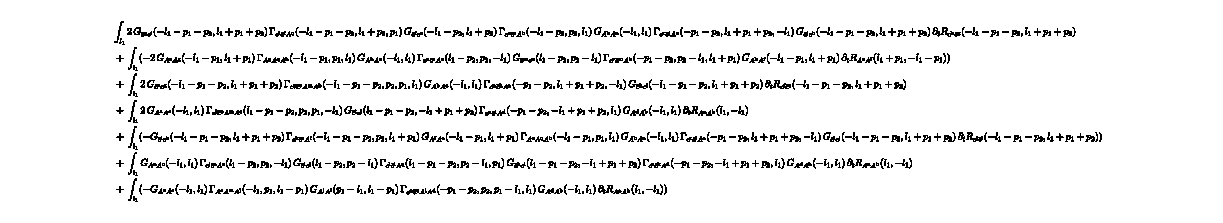

GetSuperIndexTermTransformations[<|MasterEquation→masterEquation,FieldSpace→<|cField→{A[p,{v,c}]},Grassmann→{{cb[p,{c}],c[p,{c}]}}|>,Truncation→<|GammaN→{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{A,A,cb,c}},Propagator→{{A,A},{cb,c}},Rdot→{{A,A},{cb,c}},S→{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}}|>|>,<|result→FEq[FTerm[2,Propagator[{cb,c},{{-l1-p1-p2,{c1617}},{l1+p1+p2,{c1621}}}],GammaN[{c,cb,A},{{-l1-p1-p2,{c1621}},{l1+p2,{c1628}},{p1,{v1,c1}}}],Propagator[{cb,c},{{-l1-p2,{c1628}},{l1+p2,{c1626}}}],GammaN[{c,cb,A},{{-l1-p2,{c1626}},{p2,{c2}},{l1,{v1632,c1633}}}],Propagator[{A,A},{{-l1,{v1632,c1633}},{l1,{v1623,c1624}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{l1+p1+p2,{c1630}},{-l1,{v1623,c1624}}}],Propagator[{cb,c},{{-l1-p1-p2,{c1630}},{l1+p1+p2,{c1619}}}],Rdot[{c,cb},{{-l1-p1-p2,{c1619}},{l1+p1+p2,{c1617}}}]],FTerm[-2,Propagator[{A,A},{{-l1-p1,{v1635,c1636}},{l1+p1,{v1641,c1642}}}],GammaN[{A,A,A},{{-l1-p1,{v1641,c1642}},{p1,{v1,c1}},{l1,{v1649,c1650}}}],Propagator[{A,A},{{-l1,{v1649,c1650}},{l1,{v1646,c1647}}}],GammaN[{c,cb,A},{{l1-p2,{c1655}},{p2,{c2}},{-l1,{v1646,c1647}}}],Propagator[{cb,c},{{l1-p2,{c1644}},{-l1+p2,{c1655}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{-l1+p2,{c1644}},{l1+p1,{v1652,c1653}}}],Propagator[{A,A},{{-l1-p1,{v1652,c1653}},{l1+p1,{v1638,c1639}}}],Rdot[{A,A},{{l1+p1,{v1635,c1636}},{-l1-p1,{v1638,c1639}}}]],FTerm[2,Propagator[{cb,c},{{-l1-p1-p2,{c1657}},{l1+p1+p2,{c1664}}}],GammaN[{c,cb,A,A},{{-l1-p1-p2,{c1664}},{p2,{c2}},{p1,{v1,c1}},{l1,{v1668,c1669}}}],Propagator[{A,A},{{-l1,{v1668,c1669}},{l1,{v1661,c1662}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{l1+p1+p2,{c1666}},{-l1,{v1661,c1662}}}],Propagator[{cb,c},{{-l1-p1-p2,{c1666}},{l1+p1+p2,{c1659}}}],Rdot[{c,cb},{{-l1-p1-p2,{c1659}},{l1+p1+p2,{c1657}}}]],FTerm[2,Propagator[{A,A},{{-l1,{v1671,c1672}},{l1,{v1679,c1680}}}],GammaN[{c,cb,A,A},{{l1-p1-p2,{c1685}},{p2,{c2}},{p1,{v1,c1}},{-l1,{v1679,c1680}}}],Propagator[{cb,c},{{l1-p1-p2,{c1677}},{-l1+p1+p2,{c1685}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{-l1+p1+p2,{c1677}},{l1,{v1682,c1683}}}],Propagator[{A,A},{{-l1,{v1682,c1683}},{l1,{v1674,c1675}}}],Rdot[{A,A},{{l1,{v1671,c1672}},{-l1,{v1674,c1675}}}]],FTerm[-1,Propagator[{cb,c},{{-l1-p1-p2,{c1687}},{l1+p1+p2,{c1697}}}],GammaN[{c,cb,A},{{-l1-p1-p2,{c1697}},{p2,{c2}},{l1+p1,{v1704,c1705}}}],Propagator[{A,A},{{-l1-p1,{v1704,c1705}},{l1+p1,{v1691,c1692}}}],GammaN[{A,A,A},{{-l1-p1,{v1691,c1692}},{p1,{v1,c1}},{l1,{v1699,c1700}}}],Propagator[{A,A},{{-l1,{v1699,c1700}},{l1,{v1694,c1695}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{l1+p1+p2,{c1702}},{-l1,{v1694,c1695}}}],Propagator[{cb,c},{{-l1-p1-p2,{c1702}},{l1+p1+p2,{c1689}}}],Rdot[{c,cb},{{-l1-p1-p2,{c1689}},{l1+p1+p2,{c1687}}}]],FTerm[Propagator[{A,A},{{-l1,{v1707,c1708}},{l1,{v1717,c1718}}}],GammaN[{c,cb,A},{{l1-p2,{c1725}},{p2,{c2}},{-l1,{v1717,c1718}}}],Propagator[{cb,c},{{l1-p2,{c1713}},{-l1+p2,{c1725}}}],GammaN[{c,cb,A},{{l1-p1-p2,{c1720}},{-l1+p2,{c1713}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1-p1-p2,{c1715}},{-l1+p1+p2,{c1720}}}],GammaN[{c,cb,A},{{-p1-p2,{c3}},{-l1+p1+p2,{c1715}},{l1,{v1722,c1723}}}],Propagator[{A,A},{{-l1,{v1722,c1723}},{l1,{v1710,c1711}}}],Rdot[{A,A},{{l1,{v1707,c1708}},{-l1,{v1710,c1711}}}]],FTerm[-1,Propagator[{A,A},{{-l1,{v1727,c1728}},{l1,{v1736,c1737}}}],GammaN[{A,A,A},{{-l1,{v1736,c1737}},{p1,{v1,c1}},{l1-p1,{v1742,c1743}}}],Propagator[{A,A},{{-l1+p1,{v1742,c1743}},{l1-p1,{v1733,c1734}}}],GammaN[{c,cb,A,A},{{-p1-p2,{c3}},{p2,{c2}},{-l1+p1,{v1733,c1734}},{l1,{v1739,c1740}}}],Propagator[{A,A},{{-l1,{v1739,c1740}},{l1,{v1730,c1731}}}],Rdot[{A,A},{{l1,{v1727,c1728}},{-l1,{v1730,c1731}}}]]],externalIndices→{i1→{p1,{v1,c1}},i2→{p2,{c2}},i3→{-p1-p2,{c3}}},loopMomenta→{l1}|>]

```mathematica
fields= <|
"cField"-> {
A[p,{v, c}]
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c},{A,A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
},
S->{
{A,A},{A,A,A},{A,A,A,A},
{cb,c},{cb,c,A}
}
|>;
SetTexStyles[cb->"\\bar{c}"];
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation
|>;
SetGlobalSetup[Setup];
DerivativeListAcbc={ A[i1],cb[i2],c[i3]};
TakeDerivatives[WetterichEquation,DerivativeListAcbc];
%//FTruncate//FSimplify//Route;
%//FPrint
%%//GetSuperIndexTermTransformations[Setup,#]&
```

```mathematica
Needs["QMeSderivation`"]

fRGEq = {
"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>
};
fields = <|
"bosonic"-> { 
A[p,{v, c}]
},
"fermionic"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
Truncation = {
{A,A},{cb,c},(* propagators *)
{cb,c,A},{A,A,A},{A,A,A,A} (* glue sector scatterings *)
};
SetupfRG = <|
"MasterEquation"->fRGEq,
"FieldSpace"->fields,
"Truncation"->Truncation
|>;

DerivativeListAcbc={ A[p1,{v1,a1}],cb[p2,{a2}],c[-p2-p1,{a3}]};
DiagramsAcbcsidx =DeriveFunctionalEquation[SetupfRG,DerivativeListAcbc,"OutputLevel"->"SuperindexDiagrams"]//RepeatedTiming;
%[[1]]
```

PlotSuperindexDiagram::shdw: Symbol PlotSuperindexDiagram appears in multiple contexts {QMeSderivation`Tools`,Global`}; definitions in context QMeSderivation`Tools` may shadow or be shadowed by other definitions.

0.105736